```mathematica
(***Note: Values for generating these plots are embedded within the raw data set, which is too large to upload onto the public data repository***)
```

```mathematica
v1Color=RGBColor["#ff1f5b"];
```

```mathematica
lpColor=RGBColor["#009ade"];
```

```mathematica
lmColor=RGBColor["#f28522"];
```

```mathematica
pmColor=Purple;
```

```mathematica
(*************************)
```

```mathematica
dateMouseSessionListV1={{"061222","Mouse22565","Session1"},{"061222","Mouse22565","Session2"},{"061222","Mouse22582","Session1"},{"061222","Mouse22582","Session2"},{"061422","Mouse22565","Session1"},{"061522","Mouse22582","Session1"},{"072622","Mouse23049","Session1"},{"072522","Mouse23090","Session1"},{"072822","Mouse23049","Session1"},{"072822","Mouse23004","Session1"},{"072922","Mouse23004","Session1"},{"080222","Mouse23049","Session1"}};
```

```mathematica
dateMouseSessionListLM={{"060722","Mouse22576","Session1"},{"060722","Mouse22576","Session2"},{"061522","Mouse22576","Session1"},{"062222","Mouse22577","Session1"},{"062822","Mouse23076","Session1"},{"072122","Mouse23076","Session1"},{"062222","Mouse22518","Session1"},{"062322","Mouse22518","Session1"}};
```

```mathematica
dateMouseSessionListLP={{"062222","Mouse22597","Session1"},{"062222","Mouse22597","Session2"},{"072122","Mouse23087","Session1"},{"072122","Mouse23096","Session1"},{"072122","Mouse23096","Session2"},{"073022","Mouse23087","Session1"},{"080122","Mouse23079","Session1"},{"080222","Mouse23079","Session1"},{"080122","Mouse23060","Session1"},{"080222","Mouse23060","Session1"}};
```

```mathematica
dateMouseSessionListPM={{"062222","Mouse22597","Session1"},{"062222","Mouse22597","Session2"},{"072122","Mouse23087","Session1"},{"072122","Mouse23096","Session1"},{"072122","Mouse23096","Session2"},{"073022","Mouse23087","Session1"},{"080122","Mouse23079","Session1"},{"080222","Mouse23079","Session1"},{"080122","Mouse23060","Session1"},{"080222","Mouse23060","Session1"},{"060722","Mouse22576","Session1"},{"060722","Mouse22576","Session2"},{"062222","Mouse22577","Session1"},{"062822","Mouse23076","Session1"},{"072122","Mouse23076","Session1"},{"062222","Mouse22518","Session1"},{"062322","Mouse22518","Session1"},{"061222","Mouse22565","Session1"},{"061222","Mouse22565","Session2"},{"061222","Mouse22582","Session1"},{"061222","Mouse22582","Session2"},{"061422","Mouse22565","Session1"},{"061522","Mouse22582","Session1"},{"072622","Mouse23049","Session1"},{"072522","Mouse23090","Session1"},{"072822","Mouse23004","Session1"},{"072922","Mouse23004","Session1"},{"080222","Mouse23049","Session1"}};
```

```mathematica
roisListV1=Table[Range[Length[FileNames["*",File[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionListV1[[n,1]],"/",dateMouseSessionListV1[[n,2]],"/",dateMouseSessionListV1[[n,3]],"/dFOverF0TimeSeries_CellBodies/"]]]]],{n,1,Length[dateMouseSessionListV1]}];
```

```mathematica
roisListLM=Table[Range[Length[FileNames["*",File[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionListLM[[n,1]],"/",dateMouseSessionListLM[[n,2]],"/",dateMouseSessionListLM[[n,3]],"/dFOverF0TimeSeries_CellBodies/"]]]]],{n,1,Length[dateMouseSessionListLM]}];
```

```mathematica
roisListLP=Table[Range[Length[FileNames["*",File[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionListLP[[n,1]],"/",dateMouseSessionListLP[[n,2]],"/",dateMouseSessionListLP[[n,3]],"/dFOverF0TimeSeries_CellBodies/"]]]]],{n,1,Length[dateMouseSessionListLP]}];
```

```mathematica
roisListPM=Table[Range[Length[FileNames["*",File[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionListPM[[n,1]],"/",dateMouseSessionListPM[[n,2]],"/",dateMouseSessionListPM[[n,3]],"/dFOverF0TimeSeries_CellBodies/"]]]]],{n,1,Length[dateMouseSessionListPM]}];
```

```mathematica
(***********************)
```

```mathematica
(**********************************************)
(*******Generate plots in Figure 4E****************) 
(**********************************************)
```

```mathematica
staFRV1=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionListV1[[n,1]],"/",dateMouseSessionListV1[[n,2]],"/",dateMouseSessionListV1[[n,3]],"/PMSpikeTriggeredAvgAxonActivity_FRestimates/","overallFRsta",ToString[roi],".txt"],"List"],{roi,roisListV1[[n]]}],{n,1,Length[dateMouseSessionListV1]}];
```

```mathematica
catenatedSTAfrV1=Flatten[staFRV1,1];
```

```mathematica
meanCatenatedSTAfrV1=Mean[catenatedSTAfrV1];
```

```mathematica
semCatenatedSTAfrV1=(#/Sqrt@Length[catenatedSTAfrV1])&/@StandardDeviation[catenatedSTAfrV1];
```

```mathematica
(************************************)
```

```mathematica
staFRLM=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionListLM[[n,1]],"/",dateMouseSessionListLM[[n,2]],"/",dateMouseSessionListLM[[n,3]],"/PMSpikeTriggeredAvgAxonActivity_FRestimates/","overallFRsta",ToString[roi],".txt"],"List"],{roi,roisListLM[[n]]}],{n,1,Length[dateMouseSessionListLM]}];
```

```mathematica
catenatedSTAfrLM=Flatten[staFRLM,1];
```

```mathematica
meanCatenatedSTAfrLM=Mean[catenatedSTAfrLM];
```

```mathematica
semCatenatedSTAfrLM=(#/Sqrt@Length[catenatedSTAfrLM])&/@StandardDeviation[catenatedSTAfrLM];
```

```mathematica
staFRLP=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionListLP[[n,1]],"/",dateMouseSessionListLP[[n,2]],"/",dateMouseSessionListLP[[n,3]],"/PMSpikeTriggeredAvgAxonActivity_FRestimates/","overallFRsta",ToString[roi],".txt"],"List"],{roi,roisListLP[[n]]}],{n,1,Length[dateMouseSessionListLP]}];
```

```mathematica
catenatedSTAfrLP=Flatten[staFRLP,1];
```

```mathematica
meanCatenatedSTAfrLP=Mean[catenatedSTAfrLP];
```

```mathematica
semCatenatedSTAfrLP=(#/Sqrt@Length[catenatedSTAfrLP])&/@StandardDeviation[catenatedSTAfrLP];
```

```mathematica
staFRPM=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionListPM[[n,1]],"/",dateMouseSessionListPM[[n,2]],"/",dateMouseSessionListPM[[n,3]],"/PMSpikeTriggeredAvgCBActivity_FRestimates/","overallFRstaCB",ToString[roi],".txt"],"List"],{roi,roisListPM[[n]]}],{n,1,Length[dateMouseSessionListPM]}];
```

```mathematica
catenatedSTAfrPM=Flatten[staFRPM,1];
```

```mathematica
meanCatenatedSTAfrPM=Mean[catenatedSTAfrPM];
```

```mathematica
semCatenatedSTAfrPM=(#/Sqrt@Length[catenatedSTAfrPM])&/@StandardDeviation[catenatedSTAfrPM];
```

```mathematica
(************************************************)
```

```mathematica
(***********************)
```

```mathematica
staRandFRV1=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionListV1[[n,1]],"/",dateMouseSessionListV1[[n,2]],"/",dateMouseSessionListV1[[n,3]],"/PMSpikeTriggeredAvgAxonActivity_FRestimates/","overallFRstaRand",ToString[roi],".txt"],"List"],{roi,roisListV1[[n]]}],{n,1,Length[dateMouseSessionListV1]}];
```

```mathematica
catenatedSTARfrV1=Flatten[staRandFRV1,1];
```

```mathematica
meanCatenatedSTARfrV1=Mean[catenatedSTARfrV1];
```

```mathematica
semCatenatedSTARfrV1=(#/Sqrt@Length[catenatedSTARfrV1])&/@StandardDeviation[catenatedSTARfrV1];
```

```mathematica
(************************************)
```

```mathematica
staRandFRLM=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionListLM[[n,1]],"/",dateMouseSessionListLM[[n,2]],"/",dateMouseSessionListLM[[n,3]],"/PMSpikeTriggeredAvgAxonActivity_FRestimates/","overallFRstaRand",ToString[roi],".txt"],"List"],{roi,roisListLM[[n]]}],{n,1,Length[dateMouseSessionListLM]}];
```

```mathematica
catenatedSTARfrLM=Flatten[staRandFRLM,1];
```

```mathematica
meanCatenatedSTARfrLM=Mean[catenatedSTARfrLM];
```

```mathematica
semCatenatedSTARfrLM=(#/Sqrt@Length[catenatedSTARfrLM])&/@StandardDeviation[catenatedSTARfrLM];
```

```mathematica
(************************************)
```

```mathematica
staRandFRLP=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionListLP[[n,1]],"/",dateMouseSessionListLP[[n,2]],"/",dateMouseSessionListLP[[n,3]],"/PMSpikeTriggeredAvgAxonActivity_FRestimates/","overallFRstaRand",ToString[roi],".txt"],"List"],{roi,roisListLP[[n]]}],{n,1,Length[dateMouseSessionListLP]}];
```

```mathematica
catenatedSTARfrLP=Flatten[staRandFRLP,1];
```

```mathematica
meanCatenatedSTARfrLP=Mean[catenatedSTARfrLP];
```

```mathematica
semCatenatedSTARfrLP=(#/Sqrt@Length[catenatedSTARfrLP])&/@StandardDeviation[catenatedSTARfrLP];
```

```mathematica
(*********************************)
```

```mathematica
staRandFRPM=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionListPM[[n,1]],"/",dateMouseSessionListPM[[n,2]],"/",dateMouseSessionListPM[[n,3]],"/PMSpikeTriggeredAvgCBActivity_FRestimates/","overallFRstaRandCB",ToString[roi],".txt"],"List"],{roi,roisListPM[[n]]}],{n,1,Length[dateMouseSessionListPM]}];
```

```mathematica
catenatedSTARfrPM=Flatten[staRandFRPM,1];
```

```mathematica
meanCatenatedSTARfrPM=Mean[catenatedSTARfrPM];
```

```mathematica
semCatenatedSTARfrPM=(#/Sqrt@Length[catenatedSTARfrPM])&/@StandardDeviation[catenatedSTARfrPM];
```

```mathematica
(************************************************)
```

```mathematica
(*****************************************************)
```

```mathematica
catenatedV1rawMinusShuff=catenatedSTAfrV1-catenatedSTARfrV1;
```

```mathematica
meanCatenatedV1rawMinusShuff=Mean[catenatedV1rawMinusShuff];
```

```mathematica
semCatenatedV1rawMinusShuff=(#/Sqrt@Length[catenatedV1rawMinusShuff])&/@StandardDeviation[catenatedV1rawMinusShuff];
```

```mathematica
(********************************)
```

```mathematica
catenatedLMrawMinusShuff=catenatedSTAfrLM-catenatedSTARfrLM;
```

```mathematica
meanCatenatedLMrawMinusShuff=Mean[catenatedLMrawMinusShuff];
```

```mathematica
semCatenatedLMrawMinusShuff=(#/Sqrt@Length[catenatedLMrawMinusShuff])&/@StandardDeviation[catenatedLMrawMinusShuff];
```

```mathematica
(*************************)
```

```mathematica
catenatedLPrawMinusShuff=catenatedSTAfrLP-catenatedSTARfrLP;
```

```mathematica
meanCatenatedLPrawMinusShuff=Mean[catenatedLPrawMinusShuff];
```

```mathematica
semCatenatedLPrawMinusShuff=(#/Sqrt@Length[catenatedLPrawMinusShuff])&/@StandardDeviation[catenatedLPrawMinusShuff];
```

```mathematica
(*********************************)
```

```mathematica
catenatedPMrawMinusShuff=catenatedSTAfrPM-catenatedSTARfrPM;
```

```mathematica
meanCatenatedPMrawMinusShuff=Mean[catenatedPMrawMinusShuff];
```

```mathematica
semCatenatedPMrawMinusShuff=(#/Sqrt@Length[catenatedPMrawMinusShuff])&/@StandardDeviation[catenatedPMrawMinusShuff];
```

```mathematica
(***********************************)
```

```mathematica
v1STArms=ListLinePlot[{meanCatenatedV1rawMinusShuff,meanCatenatedV1rawMinusShuff+semCatenatedV1rawMinusShuff,meanCatenatedV1rawMinusShuff-semCatenatedV1rawMinusShuff},Filling->{1->{{2},Directive[Opacity[0.2],v1Color]},1->{{3},Directive[Opacity[0.2],v1Color]},4->{{5},Directive[Opacity[0.2],v1Color]},4->{{6},Directive[Opacity[0.2],v1Color]}},PlotStyle->{{v1Color,Thickness[0.006]},Transparent,Transparent},DataRange->{-4,4},PlotRange->{{-4,4},{-0.0005,0.005}},FrameTicks->{{LinTicks[-0.0005,0.005,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-4,4,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
lmSTArms=ListLinePlot[{meanCatenatedLMrawMinusShuff,meanCatenatedLMrawMinusShuff+semCatenatedLMrawMinusShuff,meanCatenatedLMrawMinusShuff-semCatenatedLMrawMinusShuff},Filling->{1->{{2},Directive[Opacity[0.2],lmColor]},1->{{3},Directive[Opacity[0.2],lmColor]},4->{{5},Directive[Opacity[0.2],lmColor]},4->{{6},Directive[Opacity[0.2],lmColor]}},PlotStyle->{{lmColor,Thickness[0.006]},Transparent,Transparent},DataRange->{-4,4},PlotRange->{{-4,4},{-0.0005,0.005}},FrameTicks->{{LinTicks[-0.0005,0.005,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-4,4,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
lpSTArms=ListLinePlot[{meanCatenatedLPrawMinusShuff,meanCatenatedLPrawMinusShuff+semCatenatedLPrawMinusShuff,meanCatenatedLPrawMinusShuff-semCatenatedLPrawMinusShuff},Filling->{1->{{2},Directive[Opacity[0.2],lpColor]},1->{{3},Directive[Opacity[0.2],lpColor]},4->{{5},Directive[Opacity[0.2],lpColor]},4->{{6},Directive[Opacity[0.2],lpColor]}},PlotStyle->{{lpColor,Thickness[0.006]},Transparent,Transparent},DataRange->{-4,4},PlotRange->{{-4,4},{-0.0005,0.005}},FrameTicks->{{LinTicks[-0.0005,0.005,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-4,4,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
pmSTArms=ListLinePlot[{meanCatenatedPMrawMinusShuff,meanCatenatedPMrawMinusShuff+semCatenatedPMrawMinusShuff,meanCatenatedPMrawMinusShuff-semCatenatedPMrawMinusShuff},Filling->{1->{{2},Directive[Opacity[0.2],pmColor]},1->{{3},Directive[Opacity[0.2],pmColor]},4->{{5},Directive[Opacity[0.2],pmColor]},4->{{6},Directive[Opacity[0.2],pmColor]}},PlotStyle->{{pmColor,Thickness[0.006]},Transparent,Transparent},DataRange->{-4,4},PlotRange->{{-4,4},{-0.0005,0.005}},FrameTicks->{{LinTicks[-0.0005,0.005,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-4,4,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

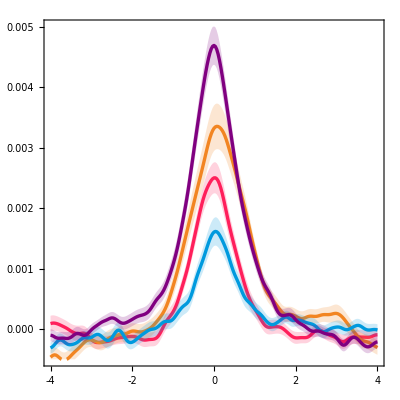

```mathematica
Show[v1STArms,lmSTArms,lpSTArms,pmSTArms]
```

```mathematica
(*******************************************)
```

```mathematica
(**********************************************)
(*******Generate plots in Figure 4E****************) 
(**********************************************)
```

```mathematica
v1PeakSizes=Table[Table[Max[staFRV1[[n,m]]]-Mean[Table[staFRV1[[n,m,i]],{i,1,60}]],{m,1,Length[roisListV1[[n]]]}],{n,1,Length[roisListV1]}];
```

```mathematica
lmPeakSizes=Table[Table[Max[staFRLM[[n,m]]]-Mean[Table[staFRLM[[n,m,i]],{i,1,60}]],{m,1,Length[roisListLM[[n]]]}],{n,1,Length[roisListLM]}];
```

```mathematica
lpPeakSizes=Table[Table[Max[staFRLP[[n,m]]]-Mean[Table[staFRLP[[n,m,i]],{i,1,60}]],{m,1,Length[roisListLP[[n]]]}],{n,1,Length[roisListLP]}];
```

```mathematica
pmPeakSizes=Table[Table[Max[staFRPM[[n,m]]]-Mean[Table[staFRPM[[n,m,i]],{i,1,60}]],{m,1,Length[roisListPM[[n]]]}],{n,1,Length[roisListPM]}];
```

```mathematica
(******)
```

```mathematica
(**********************)
```

```mathematica
v1AxonCharts=Show[BoxWhiskerChart[Flatten@v1PeakSizes,{{"Whiskers", Directive[Darker@v1Color,Thick]}, {"Fences", Directive[Darker@v1Color,Thick]},{"MedianMarker", Directive[Darker@v1Color,Thickness[0.009]]}},PlotRange->{All,{0,0.018}},ChartStyle->Directive[v1Color,Opacity[0.3]],Frame->False],DistributionChart[Flatten@v1PeakSizes,PlotRange->{All,{0,0.018}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],v1Color],Frame->False],FrameTicks->{{LinTicks[0,0.018,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
lmAxonCharts=Show[BoxWhiskerChart[Flatten@lmPeakSizes,{{"Whiskers", Directive[Darker@lmColor,Thick]}, {"Fences", Directive[Darker@lmColor,Thick]},{"MedianMarker", Directive[Darker@lmColor,Thickness[0.009]]}},PlotRange->{All,{0,0.018}},ChartStyle->Directive[lmColor,Opacity[0.3]],Frame->False],DistributionChart[Flatten@lmPeakSizes,PlotRange->{All,{0,0.018}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],lmColor],Frame->False],FrameTicks->{{LinTicks[0,0.018,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
lpAxonCharts=Show[BoxWhiskerChart[Flatten@lpPeakSizes,{{"Whiskers", Directive[Darker@lpColor,Thick]}, {"Fences", Directive[Darker@lpColor,Thick]},{"MedianMarker", Directive[Darker@lpColor,Thickness[0.009]]}},PlotRange->{All,{0,0.018}},ChartStyle->Directive[lpColor,Opacity[0.3]],Frame->False],DistributionChart[Flatten@lpPeakSizes,PlotRange->{All,{0,0.018}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],lpColor],Frame->False],FrameTicks->{{LinTicks[0,0.018,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
pmAxonCharts=Show[BoxWhiskerChart[Flatten@pmPeakSizes,{{"Whiskers", Directive[Darker@pmColor,Thick]}, {"Fences", Directive[Darker@pmColor,Thick]},{"MedianMarker", Directive[Darker@pmColor,Thickness[0.009]]}},PlotRange->{All,{0,0.018}},ChartStyle->Directive[pmColor,Opacity[0.3]],Frame->False],DistributionChart[Flatten@pmPeakSizes,PlotRange->{All,{0,0.018}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],pmColor],Frame->False],FrameTicks->{{LinTicks[0,0.018,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
transp=Show[BoxWhiskerChart[Flatten@lpPeakSizes,{{"Whiskers", Directive[Transparent,Thick]}, {"Fences", Directive[Transparent,Thick]},{"MedianMarker", Directive[Transparent,Thickness[0.009]]}},PlotRange->{All,{0,0.018}},ChartStyle->Transparent,Frame->False],DistributionChart[Flatten@lpPeakSizes,PlotRange->{All,{0,0.018}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Transparent],Frame->False],FrameTicks->{{LinTicks[0,0.018,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Black,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

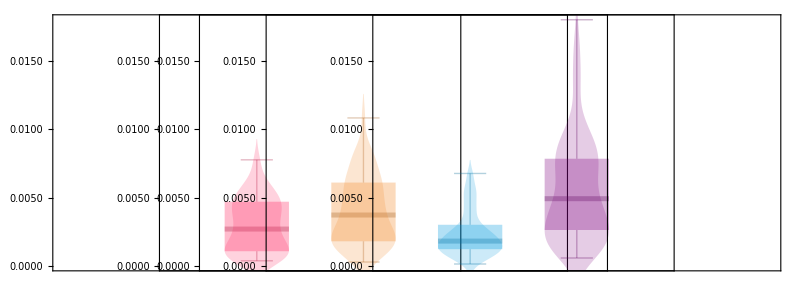

```mathematica
GraphicsRow[{v1AxonCharts,lmAxonCharts,lpAxonCharts,pmAxonCharts,transp},Spacings->{{-280,-280,-280,-280,-490}}]
```